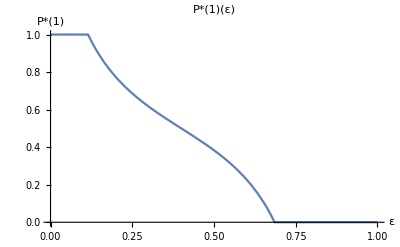
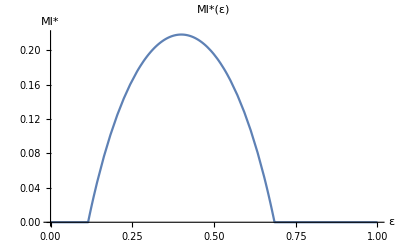

```mathematica
ClearAll["Global`*"]

λ=0.2;

τ[α_]:=λ/(1-α);

δ[α_]:=Exp[-1/τ[α]];

ε0[α_,w_]:=τ[α] Log[2/(1+Exp[-1/τ[α]])]-w;

ε1[α_,w_]:=-τ[α] Log[2/(1+Exp[1/τ[α]])]-w;

BfromEps[α_,w_,x_]:=Exp[(x+w)/τ[α]];

kStar[α_?NumericQ,B_?NumericQ]:=Module[{d=δ[α]},-((d+1) B-2)/(2 d B^2-(d+1) B)]

PHint[α_?NumericQ,B_?NumericQ]:=Module[{k=kStar[α,B],d=δ[α]},1/(1+k d B)]

PLint[α_?NumericQ,B_?NumericQ]:=Module[{k=kStar[α,B]},1/(1+k B)]

PHx[α_?NumericQ,w_?NumericQ,x_?NumericQ]:=Module[{B=BfromEps[α,w,x]},Which[x<ε0[α,w],1,x>ε1[α,w],0,True,PHint[α,B]]]

PLx[α_?NumericQ,w_?NumericQ,x_?NumericQ]:=Module[{B=BfromEps[α,w,x]},Which[x<ε0[α,w],1,x>ε1[α,w],0,True,PLint[α,B]]]
Px[α_?NumericQ,w_?NumericQ,x_?NumericQ]:=(PHx[α,w,x]+PLx[α,w,x])/2;

KL[p_,q_]:=If[p==0||p==1,0,p Log[p/q]+(1-p) Log[(1-p)/(1-q)]];

MIx[α_?NumericQ,w_?NumericQ,x_?NumericQ]:=Module[{ph,pl,p},ph=PHx[α,w,x];
pl=PLx[α,w,x];
p=(ph+pl)/2;
1/2 KL[ph,p]+1/2 KL[pl,p]]
α0=0.4;
w0=0.1;
{Plot[Evaluate[Px[α0,w0,x]],{x,0,1},PlotRange->All,AxesLabel->{"ε","P*(1)"},PlotLabel->"P*(1)(ε)"],
Plot[Evaluate[MIx[α0,w0,x]],{x,0,1},PlotRange->All,AxesLabel->{"ε","MI*"},PlotLabel->"MI*(ε)"]}


ΠI[α_?NumericQ,w_?NumericQ]:=Module[{x0=ε0[α,w],x1=ε1[α,w]},Which[
(*Case 1:full interior*)
x0>=0,
(λ*α)/(1-α)*NIntegrate[MIx[α,w,x],{x,x0,x1},Method->"GlobalAdaptive"],
(*Case 2:partial*)
x0<0<x1,
(λ*α)/(1-α)*NIntegrate[MIx[α,w,x],{x,0,x1},Method->"GlobalAdaptive"],
(*Case 3*)
True,0]]

ΠF[α_?NumericQ,w_?NumericQ]:=Module[{x0=ε0[α,w],x1=ε1[α,w]},
Which[(*Case 1:full interior*)
x0>=0,
w*NIntegrate[Px[α,w,x],{x,x0,x1},Method->"GlobalAdaptive"]+x0*w,
(*Case 2:partial*)
x0<0<x1,
w*NIntegrate[Px[α,w,x],{x,0,x1},Method->"GlobalAdaptive"],
(*Case 3*)
True,0]]
Π[α_?NumericQ,w_?NumericQ]:=ΠF[α,w]+ΠI[α,w]
```

Platform profit plots

```mathematica
makePlots[f_,title_]:=Module[{max,αstar,wstar,maxval,p3d,pcont},(*---Find maximum---*)max=NMaximize[{f[α,w],0.01<=α<=0.99&&0<=w<=1},{α,w}, Method->{"RandomSearch","SearchPoints"->50}];
maxval=max[[1]];
{αstar,wstar}={α,w}/. max[[2]];
(*---3D Plot---*)p3d=Show[Plot3D[f[α,w],{α,0.01,0.99},{w,0,1},PlotPoints->40,MaxRecursion->2,PlotRange->All,AxesLabel->{"α","w",title},PlotLabel->title],Graphics3D[{Black,PointSize[0.02],Point[{αstar,wstar,maxval}]}]];
(*---Contour Plot---*)pcont=Show[ContourPlot[f[α,w],{α,0.01,0.99},{w,0,1},Contours->20,PlotPoints->40,FrameLabel->{"α","w"},PlotLegends->Automatic],Graphics[{Black,PointSize[0.02],Point[{αstar,wstar}]}]];
{p3d,pcont}]
row1=makePlots[ΠF,"ΠF"];
row2=makePlots[ΠI,"ΠI"];
row3=makePlots[Π,"Π Total"];
GraphicsGrid[{row1,row2,row3},Spacings->{0.5,0.5}]
```

-Graphics-

```mathematica
Plot3D[ΠF[α,w],{α,0.01,0.99},{w,0,1},PlotPoints->30,MaxRecursion->2,PlotRange->All,AxesLabel->{"α","w","Π"}]
Plot3D[ΠI[α,w],{α,0.01,0.99},{w,0,1},PlotPoints->30,MaxRecursion->2,PlotRange->All,AxesLabel->{"α","w","Π"}]
Plot3D[Π[α,w],{α,0.01,0.99},{w,0,1},PlotPoints->30,MaxRecursion->2,PlotRange->All,AxesLabel->{"α","w","Π"}]
ContourPlot[ΠF[α,w],{α,0.01,0.99},{w,0,1},Contours->20,PlotPoints->30]
ContourPlot[ΠI[α,w],{α,0.01,0.99},{w,0,1},Contours->20,PlotPoints->30]
ContourPlot[Π[α,w],{α,0.01,0.99},{w,0,1},Contours->20,PlotPoints->30]
```

Welfare

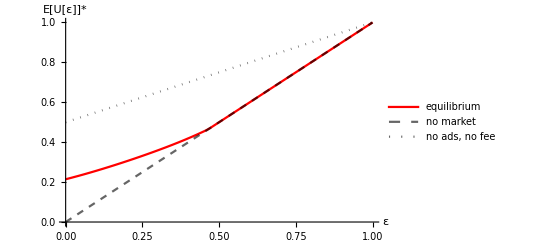

```mathematica
U[x_,w_,α_]:=Piecewise[{
{0.5-w,x<ε0[α,w]},
{0.5(PHx[α,w,x]*(1-w)+PLx[α,w,x]*(-w)+(2-PHx[α,w,x]-PLx[α,w,x])*x)-λ*MIx[α,w,x],ε0[α,w]<x<ε1[α,w]},
{x,x>ε1[α,w]}
}];
FullInfo[x_,w_]:=Piecewise[{
{1,x<-w},
{0.5,-w<x<1-w},
{0,x>1-w}
}];

Plot[{U[x,0.32,0.4],x, Max[x,(1+x)/2]},{x,0,1}, PlotRange->{0,1},PlotStyle->{Red,{Black,Dashed,Opacity[0.6]}, {Black,Dotted,Opacity[0.6]}},AxesLabel->{"ε","E[U[ε]]*"},PlotLegends->{"equilibrium","no market","no ads, no fee"}]
```

0.443461

0.0115759

0.353646

0.0728276

0.0746136

{0.337183,0.279488}

0.0101821

0.0644315

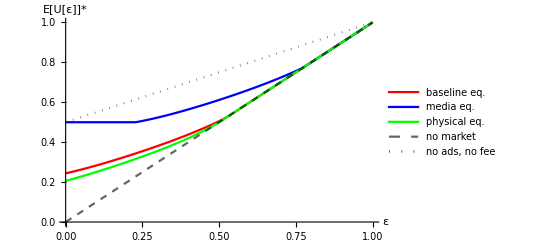

```mathematica
maxm=NMaximize[{ΠI[α,0],0.01<=α<=0.99},α,Method->{"RandomSearch","SearchPoints"->50}];
αstarm=α/. maxm[[2]] 
Pistarm=maxm[[1]] 

maxp=NMaximize[{ΠF[0,w],0.01<=w<=0.99},w,Method->{"RandomSearch","SearchPoints"->50}];
wstarp=w/. maxp[[2]] 
Pistarp=maxp[[1]] 

max=NMaximize[{Π[α,w],0.01<=α<=0.99&&0<=w<=1},{α,w},Method->{"RandomSearch","SearchPoints"->50}];
Pistar=max[[1]] 
{αstar,wstar}={α,w}/. max[[2]] 
PiIstar=ΠI[αstar,wstar] 
PiFstar=ΠF[αstar,wstar] 
Plot[{U[x,wstar,αstar],U[x,0,αstarm],U[x,wstarp,0],x,Max[x,(1+x)/2]},{x,0,1},PlotRange->{0,1},PlotStyle->{Red,Blue,Green,{Black,Dashed,Opacity[0.6]},{Black,Dotted,Opacity[0.6]}},AxesLabel->{"ε","E[U[ε]]*"},PlotLegends->{"baseline eq.","media eq.","physical eq.","no market","no ads, no fee"}]
```

```mathematica
ClearAll["Global`*"]

(*Core primitives*)

τ[α_,λ_]:=λ/(1-α);

δ[α_,λ_]:=Exp[-1/τ[α,λ]];

ε0[α_,w_,λ_]:=τ[α,λ]*Log[2/(1+Exp[-1/τ[α,λ]])]-w;

ε1[α_,w_,λ_]:=-τ[α,λ]*Log[2/(1+Exp[1/τ[α,λ]])]-w;

BfromEps[α_,w_,x_,λ_]:=Exp[(x+w)/τ[α,λ]];

(*Interior solution objects*)

kStar[α_?NumericQ,B_?NumericQ,λ_?NumericQ]:=Module[{d=δ[α,λ]},-((d+1) B-2)/(2 d B^2-(d+1) B)]

PHint[α_?NumericQ,B_?NumericQ,λ_?NumericQ]:=Module[{k=kStar[α,B,λ],d=δ[α,λ]},1/(1+k d B)]

PLint[α_?NumericQ,B_?NumericQ,λ_?NumericQ]:=Module[{k=kStar[α,B,λ]},1/(1+k B)]

(*Posterior probabilities*)

PHx[α_?NumericQ,w_?NumericQ,x_?NumericQ,λ_?NumericQ]:=Module[{B=BfromEps[α,w,x,λ]},Which[x<ε0[α,w,λ],1,x>ε1[α,w,λ],0,True,PHint[α,B,λ]]]

PLx[α_?NumericQ,w_?NumericQ,x_?NumericQ,λ_?NumericQ]:=Module[{B=BfromEps[α,w,x,λ]},Which[x<ε0[α,w,λ],1,x>ε1[α,w,λ],0,True,PLint[α,B,λ]]]

Px[α_?NumericQ,w_?NumericQ,x_?NumericQ,λ_?NumericQ]:=(PHx[α,w,x,λ]+PLx[α,w,x,λ])/2;

(*Information*)

KL[p_,q_]:=If[p==0||p==1,0,p Log[p/q]+(1-p) Log[(1-p)/(1-q)]]

MIx[α_?NumericQ,w_?NumericQ,x_?NumericQ,λ_?NumericQ]:=Module[{ph,pl,p},ph=PHx[α,w,x,λ];
pl=PLx[α,w,x,λ];
p=(ph+pl)/2;
1/2 KL[ph,p]+1/2 KL[pl,p]]
Ueq[x_?NumericQ,w_?NumericQ,α_?NumericQ,λ_?NumericQ]:=Piecewise[{{0.5-w,x<eps0[α,w,λ]},{0.5 (PHx[α,w,x,λ] (1-w)+PLx[α,w,x,λ] (-w)+(2-PHx[α,w,x,λ]-PLx[α,w,x,λ]) x)-λ MIx[α,w,x,λ],eps0[α,w,λ]<x<eps1[α,w,λ]},{x,x>eps1[α,w,λ]}}];
(*Profit functions*)
UserWelfare[α_?NumericQ,w_?NumericQ,λ_?NumericQ]:=NIntegrate[Ueq[x,w,α,λ],{x,0,1},Method->{"GlobalAdaptive","SymbolicProcessing"->0},MaxRecursion->20,AccuracyGoal->8,PrecisionGoal->8];;

ΠI[α_?NumericQ,w_?NumericQ,λ_?NumericQ]:=Module[{x0,x1},x0=ε0[α,w,λ];
x1=ε1[α,w,λ];
Which[x0>=0,(λ α)/(1-α)*NIntegrate[MIx[α,w,x,λ],{x,x0,x1},Method->"GlobalAdaptive"],x0<0<x1,(λ α)/(1-α)*NIntegrate[MIx[α,w,x,λ],{x,0,x1},Method->"GlobalAdaptive"],True,0]]

ΠF[α_?NumericQ,w_?NumericQ,λ_?NumericQ]:=Module[{x0,x1},x0=ε0[α,w,λ];
x1=ε1[α,w,λ];
Which[x0>=0,w NIntegrate[Px[α,w,x,λ],{x,x0,x1},Method->"GlobalAdaptive"]+x0 w,x0<0<x1,w NIntegrate[Px[α,w,x,λ],{x,0,x1},Method->"GlobalAdaptive"],True,0]]

Π[α_?NumericQ,w_?NumericQ,λ_?NumericQ]:=ΠF[α,w,λ]+ΠI[α,w,λ];

ProfitMedia[λ_?NumericQ]:=Module[{maxm},maxm=NMaximize[{ΠI[α,0,λ],0.01<=α<=0.99},α,Method->"NelderMead"];
maxm[[1]]]

ProfitPhysical[λ_?NumericQ]:=Module[{maxp},maxp=NMaximize[{ΠF[0,w,λ],0.01<=w<=0.99},w,Method->"NelderMead"];
maxp[[1]]]


ProfitJoint[λ_?NumericQ]:=Module[{max},max=NMaximize[{Π[α,w,λ],0.01<=α<=0.99&&0<=w<=1},{α,w},Method->"NelderMead"];
max[[1]]]
ClearAll[AllEquilibria]

AllEquilibria[λ_?NumericQ]:=Module[{media,physical,joint,αm,wp,αj,wj},(*MEDIA:w=0*)media=Quiet@Check[NMaximize[{ΠI[α,0,λ],0.01<=α<=0.99},α,Method->"NelderMead"],$Failed];
αm=If[media===$Failed,0,α/. media[[2]]];
(*PHYSICAL:α=0*)physical=Quiet@Check[NMaximize[{ΠF[0,w,λ],0.01<=w<=0.99},w,Method->"NelderMead"],$Failed];
wp=If[physical===$Failed,0,w/. physical[[2]]];
(*JOINT*)joint=Quiet@Check[NMaximize[{Π[α,w,λ],0.01<=α<=0.99&&0<=w<=1},{α,w},Method->"NelderMead"],$Failed];
If[joint===$Failed,Return[<||>]];
{αj,wj}={α,w}/. joint[[2]];
<|"AlphaMedia"->αm,"wMedia"->0,"PiIMedia"->ΠI[αm,0,λ],"PiFMedia"->0,"PiMedia"->ΠI[αm,0,λ],"RatioMedia"->ΠI[αm,0,λ]/(ΠF[αm,0,λ]+ΠI[αm,0,λ]),"AlphaPhysical"->0,"wPhysical"->wp,"PiIPhysical"->0,"PiFPhysical"->ΠF[0,wp,λ],"PiPhysical"->ΠF[0,wp,λ], "RatioPhysical"->ΠI[0,wp,λ]/(ΠF[0,wp,λ]+ΠI[0,wp,λ]),
"AlphaJoint"->αj,"wJoint"->wj,"PiIJoint"->ΠI[αj,wj,λ],"PiFJoint"->ΠF[αj,wj,λ],"PiJoint"->ΠF[αj,wj,λ]+ΠI[αj,wj,λ], "RatioJoint"->ΠI[αj,wj,λ]/(ΠF[αj,wj,λ]+ΠI[αj,wj,λ])|>]

lambdaGrid=Range[0.01,0.99,0.02];

LaunchKernels[];

results=ParallelTable[{λ,AllEquilibria[λ]},{λ,lambdaGrid}];
extract[key_]:=Table[{results[[i,1]],results[[i,2,key]]},{i,Length[results]}];
```

LaunchKernels::nodef: Some subkernels are already running. Not launching default kernels again.

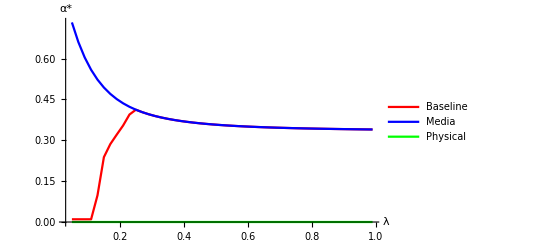

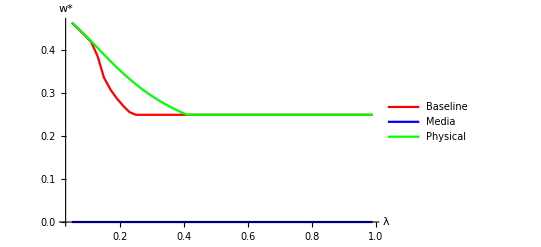

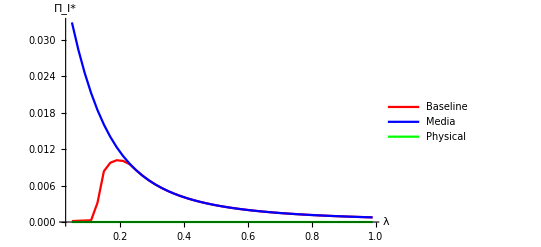

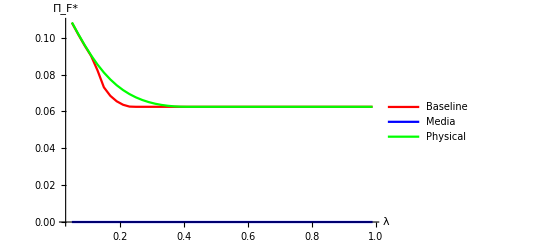

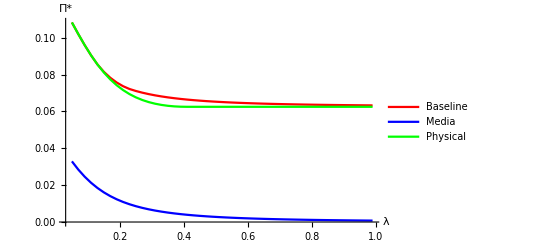

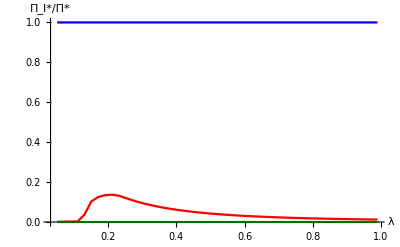

```mathematica
ListLinePlot[{extract["AlphaJoint"],extract["AlphaMedia"],extract["AlphaPhysical"]},PlotLegends->{"Baseline","Media","Physical"},AxesLabel->{"λ","α*"},PlotRange->All,PlotStyle ->{Red,Blue, Green}]
ListLinePlot[{extract["wJoint"],extract["wMedia"],extract["wPhysical"]},PlotLegends->{"Baseline","Media","Physical"},AxesLabel->{"λ","w*"},PlotRange->All,PlotStyle ->{Red,Blue, Green}]
ListLinePlot[{extract["PiIJoint"],extract["PiIMedia"],extract["PiIPhysical"]},PlotLegends->{"Baseline","Media","Physical"},AxesLabel->{"λ","Π_I*"},PlotRange->All,PlotStyle ->{Red,Blue, Green}]
ListLinePlot[{extract["PiFJoint"],extract["PiFMedia"],extract["PiFPhysical"]},PlotLegends->{"Baseline","Media","Physical"},AxesLabel->{"λ","Π_F*"},PlotRange->All,PlotStyle ->{Red,Blue, Green}]
ListLinePlot[{extract["PiJoint"],extract["PiMedia"],extract["PiPhysical"]},PlotLegends->{"Baseline","Media","Physical"},AxesLabel->{"λ","Π*"},PlotRange->All,PlotStyle ->{Red,Blue, Green}]
ListLinePlot[{extract["RatioJoint"],extract["RatioMedia"],extract["RatioPhysical"]},AxesLabel->{"λ","Π_I*/Π*"},PlotRange->All,PlotStyle ->{Red,Blue, Green}]
```

-Graphics-

-Graphics-

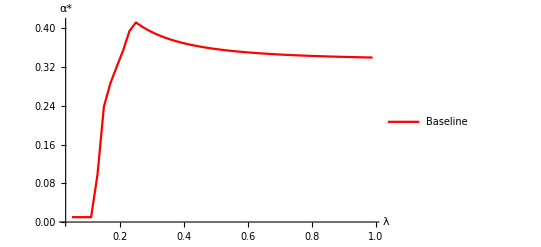

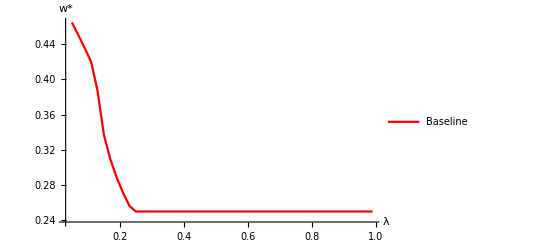

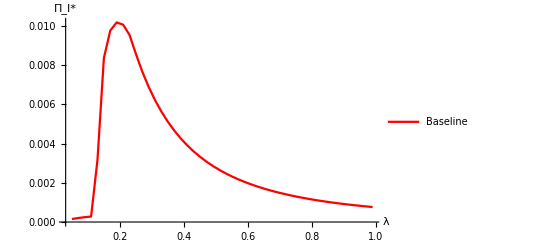

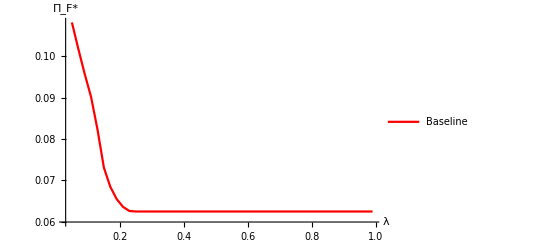

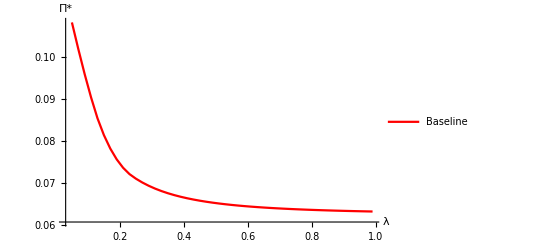

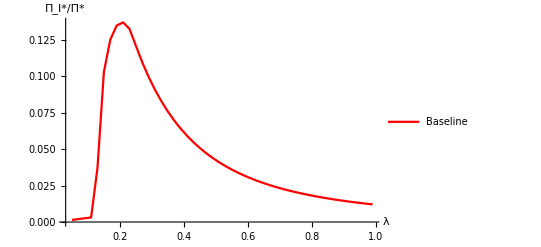

```mathematica
lambdaGrid=extract["AlphaJoint"][[All,1]];

alphaAssoc=Association[extract["AlphaJoint"]];
wAssoc=Association[extract["wJoint"]];
piAssoc=Association[extract["PiJoint"]];

userWelfareJoint=Table[{λ,UserWelfare[alphaAssoc[λ],wAssoc[λ],λ]},{λ,lambdaGrid}];

totalWelfareJoint=Table[{λ,piAssoc[λ]+UserWelfare[alphaAssoc[λ],wAssoc[λ],λ]},{λ,lambdaGrid}];
ListLinePlot[{userWelfareJoint},PlotLegends->{"Baseline"},AxesLabel->{"λ","User welfare"},PlotRange->All,PlotStyle->{Red}]

ListLinePlot[{totalWelfareJoint},PlotLegends->{"Baseline"},AxesLabel->{"λ","Total welfare"},PlotRange->All,PlotStyle->{Red}]
ListLinePlot[{extract["AlphaJoint"]},PlotLegends->{"Baseline"},AxesLabel->{"λ","α*"},PlotRange->All,PlotStyle->{Red}]

ListLinePlot[{extract["wJoint"]},PlotLegends->{"Baseline"},AxesLabel->{"λ","w*"},PlotRange->All,PlotStyle->{Red}]

ListLinePlot[{extract["PiIJoint"]},PlotLegends->{"Baseline"},AxesLabel->{"λ","Π_I*"},PlotRange->All,PlotStyle->{Red}]

ListLinePlot[{extract["PiFJoint"]},PlotLegends->{"Baseline"},AxesLabel->{"λ","Π_F*"},PlotRange->All,PlotStyle->{Red}]

ListLinePlot[{extract["PiJoint"]},PlotLegends->{"Baseline"},AxesLabel->{"λ","Π*"},PlotRange->All,PlotStyle->{Red}]

ListLinePlot[{extract["RatioJoint"]},PlotLegends->{"Baseline"},AxesLabel->{"λ","Π_I*/Π*"},PlotRange->All,PlotStyle->{Red}]
```

```mathematica
ClearAll["Global`*"];

(*----Core objects parameterized by λ----*)
tau[α_,λ_]:=λ/(1-α);
delta[α_,λ_]:=Exp[-1/tau[α,λ]];

eps0[α_,w_,λ_]:=tau[α,λ] Log[2/(1+Exp[-1/tau[α,λ]])]-w;
eps1[α_,w_,λ_]:=-tau[α,λ] Log[2/(1+Exp[1/tau[α,λ]])]-w;

BfromEps[α_,w_,x_,λ_]:=Exp[(x+w)/tau[α,λ]];

kStar[α_?NumericQ,B_?NumericQ,λ_?NumericQ]:=Module[{d=delta[α,λ]},-((d+1) B-2)/(2 d B^2-(d+1) B)];

PHint[α_?NumericQ,B_?NumericQ,λ_?NumericQ]:=Module[{k=kStar[α,B,λ],d=delta[α,λ]},1/(1+k d B)];

PLint[α_?NumericQ,B_?NumericQ,λ_?NumericQ]:=Module[{k=kStar[α,B,λ]},1/(1+k B)];

PHx[α_?NumericQ,w_?NumericQ,x_?NumericQ,λ_?NumericQ]:=Module[{B=BfromEps[α,w,x,λ],x0=eps0[α,w,λ],x1=eps1[α,w,λ]},Which[x<x0,1,x>x1,0,True,PHint[α,B,λ]]];

PLx[α_?NumericQ,w_?NumericQ,x_?NumericQ,λ_?NumericQ]:=Module[{B=BfromEps[α,w,x,λ],x0=eps0[α,w,λ],x1=eps1[α,w,λ]},Which[x<x0,1,x>x1,0,True,PLint[α,B,λ]]];

Px[α_?NumericQ,w_?NumericQ,x_?NumericQ,λ_?NumericQ]:=(PHx[α,w,x,λ]+PLx[α,w,x,λ])/2;

KL[p_,q_]:=If[p==0||p==1,0,p Log[p/q]+(1-p) Log[(1-p)/(1-q)]];

MIx[α_?NumericQ,w_?NumericQ,x_?NumericQ,λ_?NumericQ]:=Module[{ph,pl,p},ph=PHx[α,w,x,λ];
pl=PLx[α,w,x,λ];
p=(ph+pl)/2;
1/2 KL[ph,p]+1/2 KL[pl,p]];

(*----Equilibrium utility U(x;λ)----*)
Ueq[x_?NumericQ,w_?NumericQ,α_?NumericQ,λ_?NumericQ]:=Module[{x0=eps0[α,w,λ],x1=eps1[α,w,λ],ph,pl,mi},Which[x<x0,0.5-w,x>x1,x,True,ph=PHx[α,w,x,λ];
pl=PLx[α,w,x,λ];
mi=MIx[α,w,x,λ];
0.5 (ph (1-w)+pl (-w)+(2-ph-pl) x)-λ mi]];

(*----Benchmarks (unchanged)----*)
NoMarket[x_]:=x;
NoAdsNoFee[x_]:=(1+x)/2;

(*----Choose α,w and a set of λ values----*)
α0=0.4;
w0=0.32;
lambdaList={0.1,0.2,0.3,0.5,0.8};
```

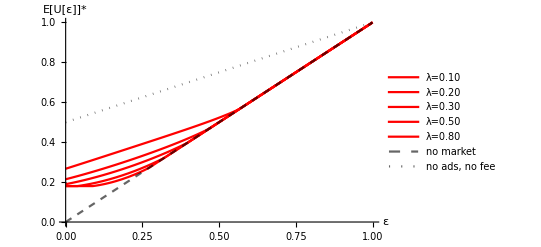

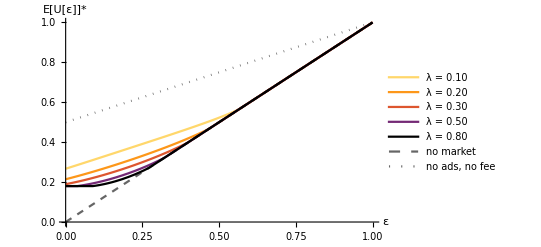

```mathematica
Plot[Evaluate@Join[Table[Ueq[x,w0,α0,λ],{λ,lambdaList}],{NoMarket[x],NoAdsNoFee[x]}],{x,0,1},PlotRange->{0,1},AxesLabel->{"ε","E[U[ε]]*"},PlotLegends->Join[Table[Row[{"λ = ",NumberForm[λ,{3,2}]}],{λ,lambdaList}],{"no market","no ads, no fee"}],PlotStyle->Join[Table[{ColorData["SunsetColors"][1-i/Length[lambdaList]],Thick},{i,Length[lambdaList]}],{{Black,Dashed,Opacity[0.6]},{Black,Dotted,Opacity[0.6]}}]]
```